# NG4P14

Разобралась студентка 2 курса  5 группы
Кадакова Надежда
18.06.2017 в 02.30 ...

## Ex.1

```mathematica
(*из 13 лабы*)
```

```mathematica
SetDirectory@NotebookDirectory[]
```

I:\Nadzeya Kadakova

```mathematica
Data=Import["NG17P14Problem.xlsx",{"Sheets", "Clout"}]⟦2;;All⟧;
```

```mathematica
Clout=Standardize@Data⟦All,3;;-1⟧;
```

```mathematica
CohanNet=Array[PadRight[{-0.5+(#1-1)/16,-0.5+(#2-1)/16,-0.5},32]&,{16,16}];
```

```mathematica
FindNearestNeuroInd[Near_]:=Flatten[{Quotient[#,16,1]+1,Mod[#,16,1]}&/@Nearest[Flatten[CohanNet,1]->"Index",Near],1];
```

```mathematica
FindNearestCloutInd[Clout_:Clout,Neuro_]:=First@Flatten[Nearest[Clout->"Index",Neuro],1]
```

```mathematica
σstart=4;
σit=2;
ηstart=0.3;
ηit=0.01;
it=5000;
t=0;
σspeed=-it/Log[σit/σstart];
ηspeed=-it/Log[ηit/ηstart];

NB[dist_]:=Exp[-dist^2/(2 σ^2)];
```

```mathematica
Do[σ=σstart Exp[-t/σspeed];
η=ηstart Exp[-t/ηspeed] ;
Near=RandomChoice@Clout;
Neuro=FindNearestNeuroInd[Near];
CohanNet=MapIndexed[#1NB[Plus@@Abs[Neuro-#2]]&,Map[Near-#&,CohanNet,{2}],{2}]η+CohanNet;
t++;
FinishDynamic[];
,it];
```

```mathematica
mean=Mean[EuclideanDistance[CohanNet⟦#⟦1⟧,#⟦2⟧⟧&@FindNearestNeuroInd[#],#]&/@Clout]
```

0.723206

```mathematica
squaremean=StandardDeviation[EuclideanDistance[CohanNet⟦#⟦1⟧,#⟦2⟧⟧&@FindNearestNeuroInd[#],#]&/@Clout]
```

0.580709

```mathematica
outerdistance=DistanceMatrix[Flatten[CohanNet,1]];
ind=Table[{i,j},{i,16},{j,16}];
innerdistance=Flatten[Table[Plus@@Abs[ind⟦i,j⟧-ind⟦k,l⟧],{i,16},{j,16},{k,16},{l,16}],1];
res=MapThread[List,{Flatten[outerdistance,1],Flatten[innerdistance,2]}];
```

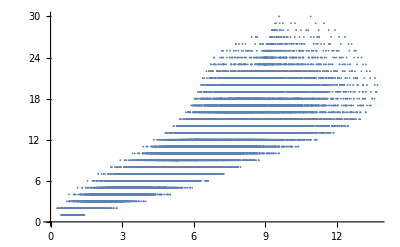

```mathematica
ListPlot@res
```

```mathematica
innermeanres=(Plus@@res⟦All,1⟧)/(Length@res);
outermeanres=(Plus@@res⟦All,2⟧)/(Length@res);
Correl=(Plus@@((#⟦1⟧-innermeanres)(#⟦2⟧-outermeanres)&/@res))/(√(Plus@@((#⟦1⟧-innermeanres)^2&/@res)Plus@@((#⟦2⟧-outermeanres)^2&/@res)))
```

0.864881

```mathematica
Correlation[res]⟦1,2⟧
```

0.864881

Заметная теснота корреляционной связи

## Ex.2

```mathematica
(*список, содержащий информацию о принадлежности узла сети к какому-либо классу и его вес. находится посредством нахождения ближайших точек к узлам из набора*)
```

```mathematica
map=MapThread[List,{Flatten[ind,1],Data⟦FindNearestCloutInd[#]&/@Flatten[CohanNet,1],1;;2⟧}];
```

```mathematica
(*ректангл рисует прямоугольник, для которого мы указываем левый нижний угол.*)
```

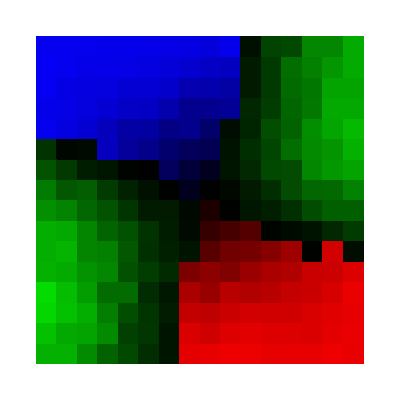

```mathematica
Graphics[{Hue[Which[#⟦2,1⟧==1,1,#⟦2,1⟧==2,0.67,#⟦2,1⟧==3,0.33],1,#⟦2,2⟧],Rectangle[#⟦1⟧]}&/@map]
```

## Ex.3

```mathematica
(*с помощью PCA вычисляем 6 главных компонент наора Clout *)
```

```mathematica
PCA=PrincipalComponents[Clout]⟦1;;6⟧;
```

```mathematica
(*проектируем. для этого все точки из набора (каждую) умножаем на каждую нглавную компоненту и получаем координаты в проективной плоскости*)
```

```mathematica
Clout3D=Table[Clout⟦i⟧.#&/@PCA⟦1;;3⟧,{i,Length@Clout}];
```

```mathematica
Graphics3D[{Hue[Which[#⟦2,1⟧==1,1,#⟦2,1⟧==2,0.67,#⟦2,1⟧==3,0.33],1,#⟦2,2⟧],Point[#⟦1⟧]}&/@MapThread[List,{Clout3D,Data⟦All,1;;2⟧}]]
```

-Graphics3D-

```mathematica
(*то же самое только для  2д*)
```

```mathematica
Clout2D=Table[Clout⟦i⟧.#&/@PCA⟦1;;2⟧,{i,Length@Clout}];
```

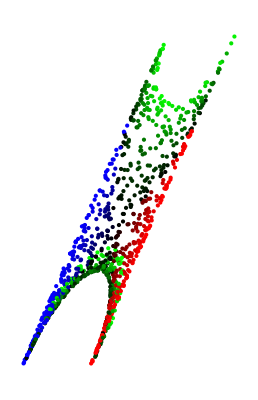

```mathematica
Graphics[{Hue[Which[#⟦2,1⟧==1,1,#⟦2,1⟧==2,0.67,#⟦2,1⟧==3,0.33],1,#⟦2,2⟧],Point[#⟦1⟧]}&/@MapThread[List,{Clout2D,Data⟦All,1;;2⟧}]]
```

## Ex.5

```mathematica
(*импоортируем характеристики животного. Транспонируем, ибо характеристики почему-то идут по столбикам*)
```

```mathematica
Animal=Import["NG17P14Problem.xlsx",{"Sheets", "Animal"}]⟦2;;All,3;;-1⟧ᵀ;
```

```mathematica
(*дополняем список характеристик значениями 0.2 до 29. Характеристик 13, дополняем до 29 16-ю*)
```

```mathematica
matr=Join[Animal,Table[0.2,{16},{16}],2];
```

```mathematica
(*строим сеть Кохонена. Сеть Кохонена 2мерная, а координаты у нас в 29-мерном пространстве*)
```

```mathematica
CohanmatrNet=Array[PadRight[{(#1-1)/16,(#2-1)/16,0},29]&,{10,10}];
```

```mathematica
(*у меня есть фазовое пространство. Для какой-то точки в этом пространстве находим ближайший узел и тенем*)
```

```mathematica
FindNearestmatrNeuroInd[Near_]:=Flatten[{Quotient[#,10,1]+1,Mod[#,10,1]}&/@Nearest[Flatten[CohanmatrNet,1]->"Index",Near],1];
```

```mathematica
(*обратная операция. для узла сети мы находим, какое животное этому узлу соответствует*)
```

```mathematica
FindNearestmatrAnimalInd[Clout_:matr,Neuro_]:=First@Nearest[Clout->"Index",Neuro];
```

```mathematica
(*задаем параметры*)
```

```mathematica
σstart=3;
σit=1.25;
ηstart=0.1;
ηit=0.01;
it=5000;
t=0;
σspeed=-it/Log[σit/σstart];
ηspeed=-it/Log[ηit/ηstart];

NB[dist_]:=Exp[-dist^2/(2 σ^2)];
```

```mathematica
Do[σ=σstart Exp[-t/σspeed];
η=ηstart Exp[-t/ηspeed] ;
Near=RandomChoice@matr;
Neuro=FindNearestmatrNeuroInd[Near];
CohanmatrNet=MapIndexed[#1NB[Plus@@Abs[Neuro-#2]]&,Map[Near-#&,CohanmatrNet,{2}],{2}]η+CohanmatrNet;
t++;
FinishDynamic[];
,it];
```

```mathematica
(*массив индексов двумерной сети кохонена*)
```

```mathematica
index=Array[{#1,#2}&,{10,10}];
```

```mathematica
(*загружаем имена животных*)
```

```mathematica
AnimalName=Import["NG17P14Problem.xlsx",{"Sheets", "Animal"}]⟦1,3;;All⟧;
```

```mathematica
(*рисуем узлы, и подписываем их. в точке с самым сильным откликом делаем надпись, к какому классу она принадежит. для этого для всех животных находим ближайший узел, прикрепляем  помощью mapthread их  к их именам. удаляем дубликаты по узлам.*)
```

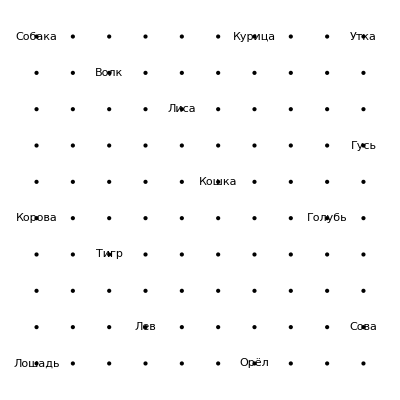

```mathematica
Show[Graphics[{Point[#]}&/@Flatten[index,1]],
(*text выводит текст в заданной точке*)
Graphics[{Text[#⟦2⟧,#⟦1⟧]}&/@DeleteDuplicatesBy[MapThread[List,{FindNearestmatrNeuroInd[#]&/@matr,AnimalName}],First]]]
```

```mathematica
(*теперь мы наоборот для узлов CohanmatrNet ищем индексы животных (FindNearestmatrAnimalInd), и по этому индексу находим имя животного*)
```

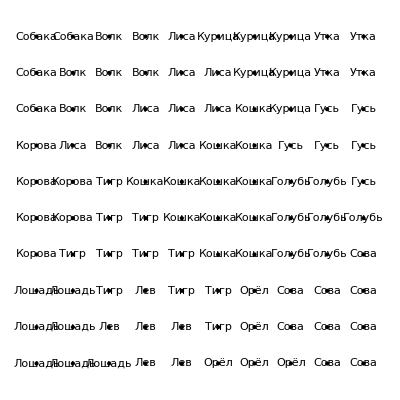

```mathematica
Show[Graphics[{Point[#]}&/@Flatten[index,1]],Graphics[{Text[#⟦2⟧,#⟦1⟧]}&/@MapThread[List,{Flatten[index,1],AnimalName⟦FindNearestmatrAnimalInd[#]&/@Flatten[CohanmatrNet,1]⟧}]]]
```